```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"](*Requires Internet Connection*)
```

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

## Collision Models

```mathematica
H = g(kron[σp,σm]+kron[σm,σp]);
U = MatrixExp[-ⅈ H];
ψ0 = {0,1};
ρ0 = out[ψ0,ψ0];
ρA = MatrixExp[-β σz]/Tr[MatrixExp[-β σz]];
```

```mathematica
g = 0.1;
β = 0.3;
nCol = 1000;
ρlist = CollisionMap[ρ0,U,ρA,nCol]//Chop;
```

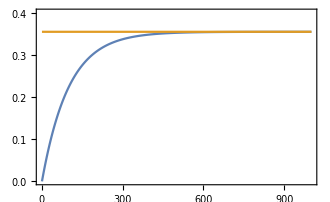

```mathematica
ListPlot[{Table[ρlist[[i]][[1,1]],{i,nCol+1}],ConstantArray[ρA[[1,1]],nCol+1]},Joined->True,PlotRange->{0,0.4}]
```

```mathematica
?CollisionMap
```

```mathematica
?out
```

```mathematica
?CollisionModelSteadyState
```

```mathematica
Clear[β,g]
CollisionModelSteadyState[U,ρA](*The LinearSolve fails here because it doesn't know how to evaluate Conjugate[Cos[g]]*)
```

LinearSolve::nosol: Linear equation encountered that has no solution.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of ….

Transpose[Partition[LinearSolve[{{-1+ⅇ^-β/(ⅇ^-β+ⅇ^β)+(ⅇ^β Conjugate[Cos[g]] Cos[g])/(ⅇ^-β+ⅇ^β),0,0,(ⅇ^-β Conjugate[Sin[g]] Sin[g])/(ⅇ^-β+ⅇ^β)},{0,-1+(ⅇ^β Conjugate[Cos[g]])/(ⅇ^-β+ⅇ^β)+(ⅇ^-β Cos[g])/(ⅇ^-β+ⅇ^β),0,0},{0,0,-1+(ⅇ^-β Conjugate[Cos[g]])/(ⅇ^-β+ⅇ^β)+(ⅇ^β Cos[g])/(ⅇ^-β+ⅇ^β),0},{(ⅇ^β Conjugate[Sin[g]] Sin[g])/(ⅇ^-β+ⅇ^β),0,0,-1+ⅇ^β/(ⅇ^-β+ⅇ^β)+(ⅇ^-β Conjugate[Cos[g]] Cos[g])/(ⅇ^-β+ⅇ^β)},{1,0,0,1}},SparseArray[…]],√2]]

```mathematica
?AnalyticalSteadyState
```

```mathematica
Clear[AnalyticalSteadyState]
AnalyticalSteadyState[ℒ_]:=Module[{ℒ2,d,ρ},d=Length[ℒ];ℒ2=Normal[Join[ℒ,{Vec[Eye[√d]]}]];ρ=Unvec[LinearSolve[ℒ2//cf,Eye[d+1]⟦-1⟧]];ρ](*Here we redefine the function so that it removes the "Conjugates" that are causing trouble above*)
```

```mathematica
Clear[β,g]
CollisionModelSteadyState[U,ρA](*now we can find the steady state*)
```

{{1/2 (1-Tanh[β]),0},{0,1/2 (1+Tanh[β])}}

```mathematica
ρA//cf(*we see that the steady state is equal to ρA*)
```

{{1/(1+ⅇ^(2 β)),0},{0,1/2 (1+Tanh[β])}}

## Collisional Quantum Thermometry

#### Recreating Fig 2 from arXiv:1904.12551

```mathematica
?AmplitudeDamping
```

```mathematica
?AmplitudeDampingKrausOperators
```

#### The amplitude damping channel results in the mater equation in Eq. (7) in the paper when the inputs are as below

```mathematica
pop = n/(1+2n);
rate = 1-ⅇ^(-((1+2n)γ));
AmplitudeDamping[pop,rate][ρ0]
```

{{((1-ⅇ^(-((1+2 n) γ))) n)/(1+2 n),0},{0,1-n/(1+2 n)+(ⅇ^(-((1+2 n) γ)) n)/(1+2 n)}}

```mathematica
ρE = DiagonalMatrix[{pop,1-pop}];(*This is the thermal state at temperature T with n defined under Eq. (7) in the paper*)
PTr[U.kron[ρ0,ρE].ConjugateTranspose[U],{2}]//cf(*The amplitude damping channel can also be modeled by the collision model defined in the previous section*)
```

{{(n Sin[g]^2)/(1+2 n),0},{0,(1+n+n Cos[g]^2)/(1+2 n)}}

```mathematica
Solve[((1-ⅇ^(-((1+2 n) γ))) n)/(1+2 n)==(n Sin[g]^2)/(1+2 n),g](*We solve for the value of g that gives us the amplitude damping channel we want*)
```

{{g→ConditionalExpression[-ArcSin[√(1-ⅇ^(-((1+2 n) γ)))]+2 π C[1], C[1]∈ℤ]},{g→ConditionalExpression[π-ArcSin[√(1-ⅇ^(-((1+2 n) γ)))]+2 π C[1], C[1]∈ℤ]},{g→ConditionalExpression[ArcSin[√(1-ⅇ^(-((1+2 n) γ)))]+2 π C[1], C[1]∈ℤ]},{g→ConditionalExpression[π+ArcSin[√(1-ⅇ^(-((1+2 n) γ)))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
UAD = U/.g->ArcSin[√(1-ⅇ^(-((1+2 n) γ)))]//cf;
```

### Ancilla ground

```mathematica
ψA = {0,1};
ρA =out[ψA,ψA];(*In Fig 1(a) the ancillas are in the groud state*)
```

```mathematica
ρAE = kron[ρA,ρE];(*CollisionModelSteadyState can only take one ancilla state and one unitary so we need to combine*)
USS = kron[UAD,σ0].kron[σ0,SWAP[]].kron[U,σ0];(*Collision first then thermalize, as in Eq. (2)*)
```

```mathematica
ρSS = CollisionModelSteadyState[USS,ρAE]//cf
```

{{-(2 (-1+ⅇ^(γ+2 n γ)) n)/((1+2 n) (1-2 ⅇ^(γ+2 n γ)+Cos[2 g])),0},{0,1+(2 (-1+ⅇ^(γ+2 n γ)) n)/((1+2 n) (1-2 ⅇ^(γ+2 n γ)+Cos[2 g]))}}

```mathematica
ρAafter = PTr[U.kron[ρSS,ρA].ConjugateTranspose[U],{1}]//cf;(*We are performing measurements on the ancillas, not the system so we want to trace out the system this time*)
dρAafter = D[ρAafter,n]//cf;
```

```mathematica
QFA = QuantumFisherInformation[ρAafter,dρAafter]//cf;
```

```mathematica
QFth = 1/(n(n+1)(2n+1)^2);(*This is just a simpler version of how this is defined in the paper*)
```

```mathematica
(QFA/QFth)/.g->π/2//cf(*You can check that is is equal to Eq. (8)*)
```

((1+n) (-1+ⅇ^(γ+2 n γ)+2 n (1+2 n) γ)^2)/((-1+ⅇ^(γ+2 n γ)) (n+ⅇ^(γ+2 n γ) (1+n)))

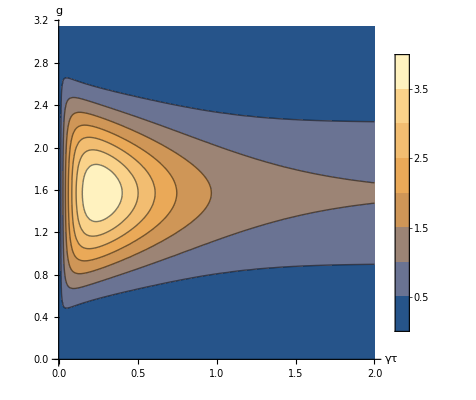

```mathematica
n = 1.514;
ContourPlot[QFA/QFth,{γ,0,2},{g,0,π},PlotLegends->Automatic,Frame->False,Axes->True,AxesLabel->{"γτ","g"}](*Fig 2. (a)*)
Clear[n]
```

### Ancilla plus

#### Exactly the same as above but with plus ancilla and sf instead of cf

```mathematica
ψA = {1/Sqrt[2],1/Sqrt[2]};
ρA =out[ψA,ψA];
```

```mathematica
ρAE = kron[ρA,ρE];
USS = kron[UAD,σ0].kron[σ0,SWAP[]].kron[U,σ0];(*Collision first then thermalize*)
```

```mathematica
?cf
```

```mathematica
sf[expr_]:=Simplify[expr,Thread[DeleteDuplicates[Cases[Normal[expr],_Symbol,∞]]>0]](*the FullSimplify in cf takes too long here so we define a new function with Simplify instead*)
```

```mathematica
ρSS = CollisionModelSteadyState[USS,ρAE]//sf;
```

```mathematica
ρAafter = PTr[U.kron[ρSS,ρA].ConjugateTranspose[U],{1}]//sf;
dρAafter = D[ρAafter,n]//sf;
```

```mathematica
QFA = QuantumFisherInformation[ρAafter,dρAafter]//sf;
```

```mathematica
QFth = 1/(n(n+1)(2n+1)^2);
```

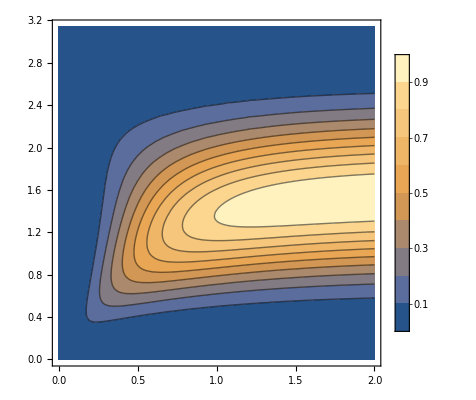

```mathematica
n = 1.514;
ContourPlot[QFA/QFth,{γ,0,2},{g,0,π},PlotLegends->Automatic](*Fig. 2 (b)*)
Clear[n]
```